```mathematica
w=NDSolve[{D[u[x,y,t],t,t]==0.001*(D[u[x,y,t],x,x]+D[u[x,y,t],y,y]),u[0,y,t]==0,u[2,y,t]==0,u[x,0,t]==0,u[x,2,t]==0,u[x,y,0]==0.2*E^(-1*((x-1)^2+(y-1)^2)/0.01)},u,{x,0,2},{y,0,2},{t,0,6}]
```

{{u→InterpolatingFunction[{{0., 2.}, {0., 2.}, {0., 6.}}, <>]}}

```mathematica
gif=Table[Plot3D[Evaluate[u[x,y,t]/. w],{x,0,2},{y,0,2},AxesLabel->Automatic,PlotRange->{{0,2},{0,2},{-0.5,0.5}}], {t,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Export["~/Desktop/Smooth.gif",gif]
```

~/Desktop/Smooth.gif

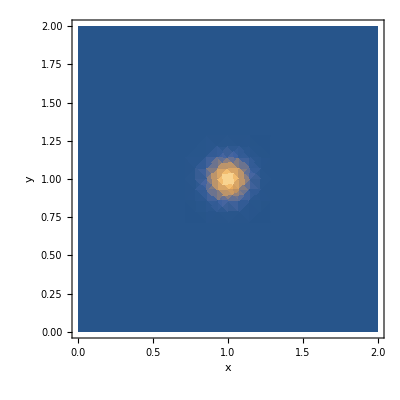
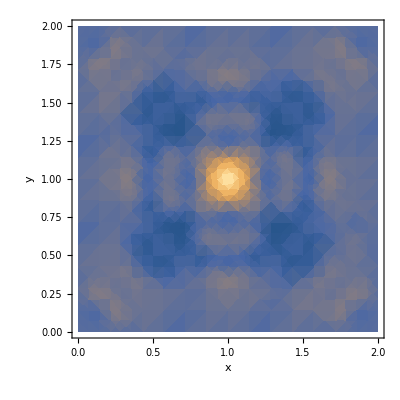
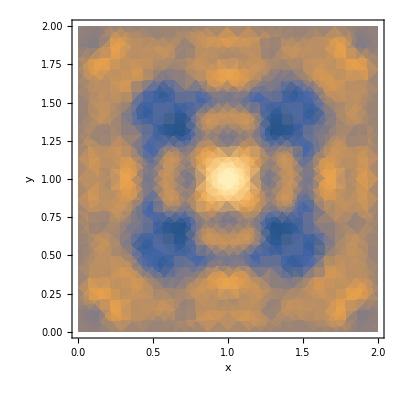
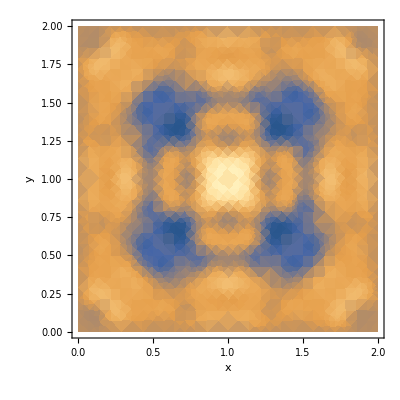
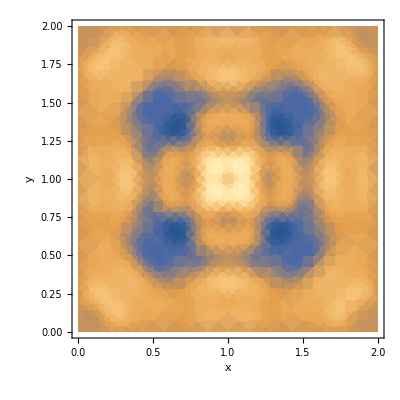
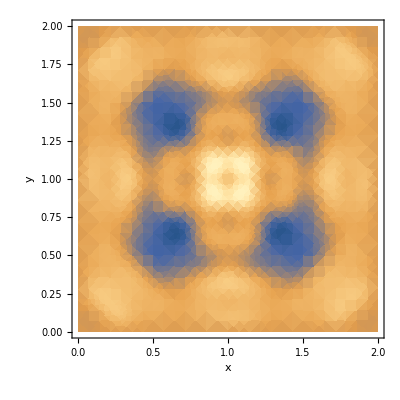
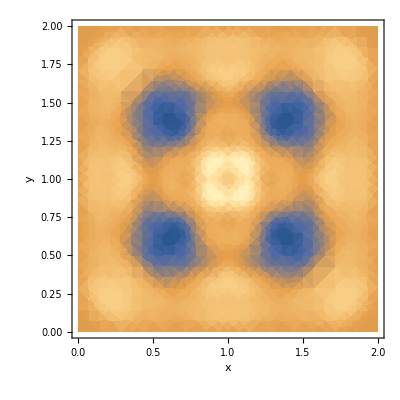
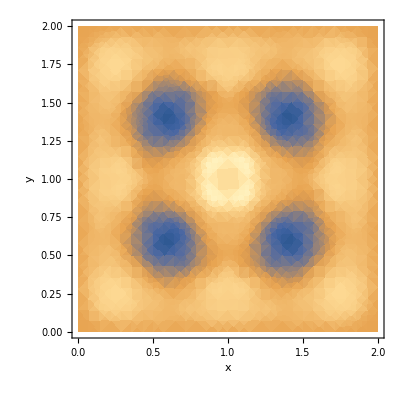

```mathematica
gif2=Table[DensityPlot[Evaluate[u[x,y,t]/. w],{x,0,2},{y,0,2},AxesLabel->Automatic,PlotRange->{{0,2},{0,2},{-0.5,0.5}}], {t,0,5,0.5}]
```

```mathematica
Export["~/Desktop/Smooth2.gif",gif2]
```

~/Desktop/Smooth2.gif